```mathematica
K2meV=0.086173324;
K2eV=K2meV/1000;
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/FRENKEL_RESULTS/Tall/Frenkel_Tall"];
fileFFE={"e0.out.m","e0_FS.out.m","VFE.Fqh_FS.out.m","VFE.Fqh_Fel_FS.out.m","VFE.Fqh_Fel.out.m","VFE.Fqh.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number}],{i,1,4}];
```

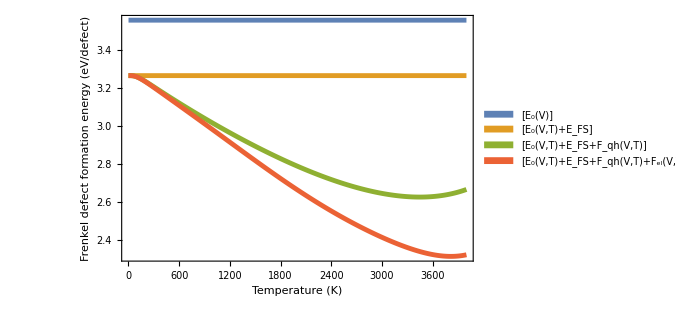

```mathematica
ListLinePlot[FFEdata,FrameLabel->{Style["Temperature (K)",15],Style["Frenkel defect formation energy (eV/defect)",15]},PlotStyle->Thickness[0.007],FrameTicksStyle->15,Frame->True,ImageSize->500,PlotLegends->Placed[SwatchLegend[{Style["[E_0(V)]",15],Style["[E_0(V,T)+_E_FS]",15],Style["[E_0(V,T)+E_FS+F_qh(V,T)]",15],Style["[E_0(V,T)+E_FS+F_qh(V,T)+F_el(V,T)]",15]}],{0.72,0.57}]]
```

```mathematica
(*Gibbs and temperature lists*)
gibbs=Transpose[FFEdata[[4]]][[2]];
ttemp=Transpose[FFEdata[[4]]][[1]];
(*Multiplicity*)
m1=24;m2=3;m3=12;
```

```mathematica
(*Trimer is lowest energy defect at 3.622, trimer is next 4.010 then 4.628 *)
deltaDimerBound=3.624-4.010;

deltaDimerUnbound=3.624-4.557;
deltaTrimerUnbound=3.624-4.628;
deltaTetramerUnbound=3.624-4.688;
```

```mathematica
(*Bound Trimer concentration*)
tgibbsTrimerBound=Transpose@{ttemp,100*m1*Exp[-gibbs/(K2eV*ttemp)]};
(*Bound Dimer*)
tgibbsDimerBound=Transpose@{ttemp,100*m1*Exp[-(gibbs-deltaDimer)/(K2eV*ttemp)]};

(*Unbound dimer*)
tgibbsDimerUnbound=Transpose@{ttemp,100*m2^0.5*Exp[-(gibbs-deltaDimerUnbound)/(2K2eV*ttemp)]};
(*Unbound Trimer*)
tgibbsTrimerUnbound=Transpose@{ttemp,100*m3^0.5*Exp[-(gibbs-deltaTrimerUnbound)/(2K2eV*ttemp)]};
(*Unbound Tetramer*)
tgibbsTetramerUnbound=Transpose@{ttemp,100*m3^0.5*Exp[-(gibbs-deltaTetramerUnbound)/(2K2eV*ttemp)]};
(*T gibbs total*)
tgibbsTotal=Transpose@{ttemp,Transpose[tgibbsTrimerBound][[2]]+Transpose[tgibbsDimerBound][[2]]+Transpose[tgibbsDimerUnbound][[2]]+Transpose[tgibbsTrimerUnbound][[2]]+Transpose[tgibbsTetramerUnbound][[2]]};
```

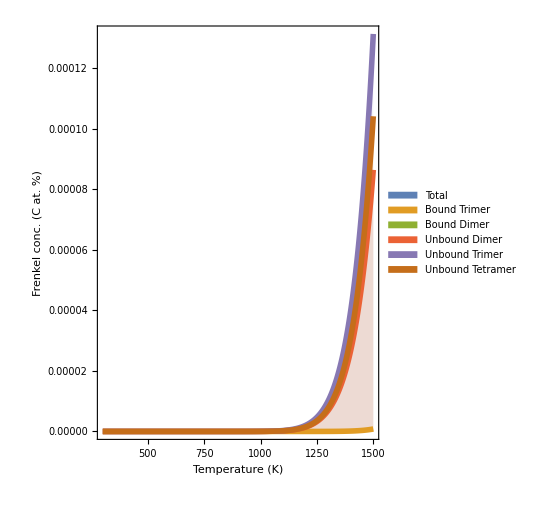

```mathematica
upper=1500;lower=300;

a=tgibbsTrimerBound[[lower;;upper]];
b=tgibbsDimerBound[[lower;;upper]];
c=tgibbsDimerUnbound[[lower;;upper]];
d=tgibbsTrimerUnbound[[lower;;upper]];
e=tgibbsTetramerUnbound[[lower;;upper]];
f=tgibbsTotal[[lower;;upper]];

plotf1=ListLinePlot[{f,a,b,c,d,e},PlotStyle->Thickness[0.01],Filling->Bottom,FillingStyle->Opacity[0.09],FrameTicksStyle->18,FrameLabel->{Style["Temperature (K)",18],Style["Frenkel conc. (C at. %)",18]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18],Style["Bound Trimer",18],Style["Bound Dimer",18],Style["Unbound Dimer",18],Style["Unbound Trimer",18],Style["Unbound Tetramer",18]}],{0.3,0.80}],AspectRatio->1.3,PlotRange->All]
```

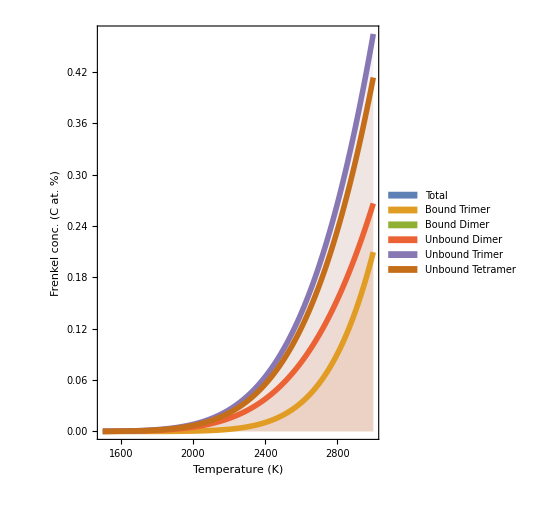

```mathematica
upper=3000;lower=1500;

a=tgibbsTrimerBound[[lower;;upper]];
b=tgibbsDimerBound[[lower;;upper]];
c=tgibbsDimerUnbound[[lower;;upper]];
d=tgibbsTrimerUnbound[[lower;;upper]];
e=tgibbsTetramerUnbound[[lower;;upper]];
f=tgibbsTotal[[lower;;upper]];

plotf2=ListLinePlot[{f,a,b,c,d,e},PlotStyle->Thickness[0.01],Filling->Bottom,FillingStyle->Opacity[0.09],FrameTicksStyle->18,FrameLabel->{Style["Temperature (K)",18],Style["Frenkel conc. (C at. %)",18]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18],Style["Bound Trimer",18],Style["Bound Dimer",18],Style["Unbound Dimer",18],Style["Unbound Trimer",18],Style["Unbound Tetramer",18]}],{0.3,0.80}],AspectRatio->1.3,PlotRange->All]
```

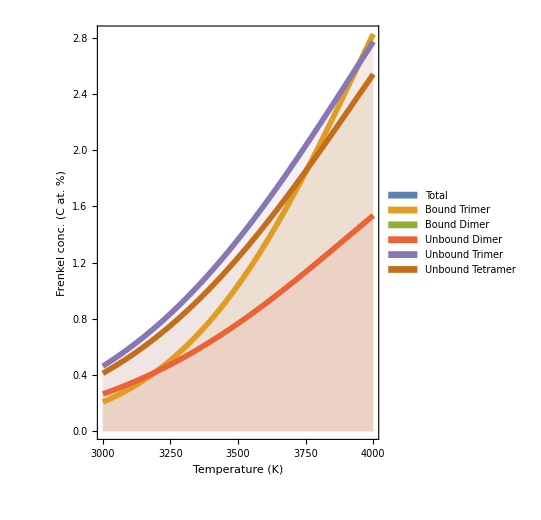

```mathematica
upper=4000;lower=3000;

a=tgibbsTrimerBound[[lower;;upper]];
b=tgibbsDimerBound[[lower;;upper]];
c=tgibbsDimerUnbound[[lower;;upper]];
d=tgibbsTrimerUnbound[[lower;;upper]];
e=tgibbsTetramerUnbound[[lower;;upper]];
f=tgibbsTotal[[lower;;upper]];

plotf3=ListLinePlot[{f,a,b,c,d,e},PlotStyle->Thickness[0.01],Filling->Bottom,FillingStyle->Opacity[0.09],FrameTicksStyle->18,FrameLabel->{Style["Temperature (K)",18],Style["Frenkel conc. (C at. %)",18]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18],Style["Bound Trimer",18],Style["Bound Dimer",18],Style["Unbound Dimer",18],Style["Unbound Trimer",18],Style["Unbound Tetramer",18]}],{0.3,0.80}],AspectRatio->1.3,PlotRange->All]
```

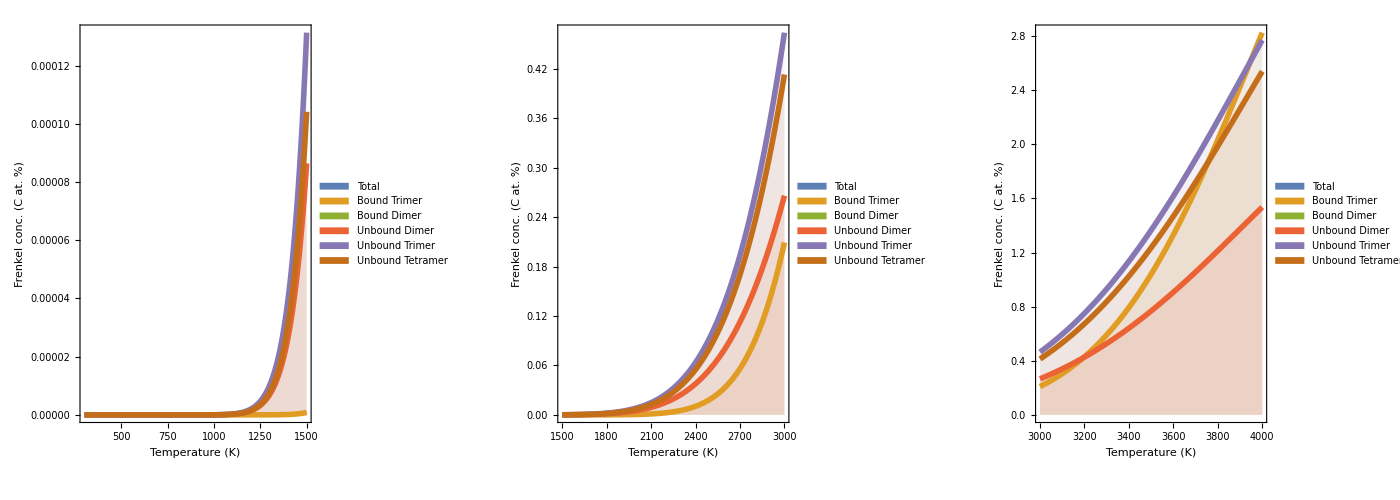

```mathematica
GraphicsGrid[{{plotf1,plotf2,plotf3}},ImageSize->{1400,500}]
```